Background

```mathematica
coord ={t,r};
metric=({{r^2-1, 0}, {0, 1/(1-r^2)}});
```

```mathematica
$Assumptions= And[t∈Reals,r>0,r<1,ω∈Reals];
metricsign=-1;
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<diffgeo.m
```

```mathematica
EEstep1 = RicciTensor-1/2 RicciScalar*metric  + Λ* metric;
```

```mathematica
EEstep2 = EEstep1  /.Λ ->(d(d-1))/2/.d->1//Simplify
```

{{0,0},{0,0}}

```mathematica
Riemann;
```

```mathematica
contract[lower[Riemann,{4}]**lower[Riemann,{4}],{1,5},{2,6},{3,7},{4,8}]
```

4

Perturbation

```mathematica
Φ=Exp[-ⅈ*ω*t]*ϕ[r]
```

ⅇ^(-ⅈ t ω) ϕ[r]

```mathematica
f[r_]=((1-r^2)r^(d-1)ϕ'[r]);
SEstep1 = -r^(1-d)f'[r] //FullSimplify;
SEstep2 = Collect[SEstep1,{ϕ''[r],ϕ'[r],ϕ[r]},Simplify]+((l(l+d-2))/r^2-ω^2/(1-r^2))ϕ[r]
```

((l (-2+d+l))/r^2-ω^2/(1-r^2)) ϕ[r]+((1-d)/r+r+d r) ϕ'[r]+(-1+r^2) ϕ''[r]

```mathematica
Solution1=Values[DSolve[SEstep2==0,ϕ[r],r]][[1]][[1]]//FullSimplify
```

((-r)^-l (ⅈ r)^-d (-1+r^2)^(-1/2 ⅈ (ⅈ+ω)) (-r^2 C[2] Hypergeometric2F1[1/2 (2-l-ⅈ ω),1/2 (2-d-l-ⅈ ω),2-d/2-l,r^2]+(-1)^l ⅈ^d r^(d+2 l) C[1] Hypergeometric2F1[1/2 (l-ⅈ ω),1/2 (d+l-ⅈ ω),d/2+l,r^2]))/(√(1-r^2))

```mathematica
SolutionR=(1-r^2)^((-ⅈ ω)/2)r^l Hypergeometric2F1[1/2 (l-ⅈ ω),1/2 (d+l-ⅈ ω),d/2+l,r^2]
SolutionNR=(1-r^2)^((-ⅈ ω)/2)r^(2-d-l)Hypergeometric2F1[1/2 (2-l-ⅈ ω),1/2 (2-d-l-ⅈ ω),2-d/2-l,r^2]
```

r^l (1-r^2)^(-(ⅈ ω)/2) Hypergeometric2F1[1/2 (l-ⅈ ω),1/2 (d+l-ⅈ ω),d/2+l,r^2]

r^(2-d-l) (1-r^2)^(-(ⅈ ω)/2) Hypergeometric2F1[1/2 (2-l-ⅈ ω),1/2 (2-d-l-ⅈ ω),2-d/2-l,r^2]

```mathematica
OriginBehaviour=Series[Solution1,{r,0,2}] //FullSimplify
```

r^(-d-l) (-ⅈ ⅇ^(1/2 π (-ⅈ (d+2 l)+ω)) C[2] r^2+O[r]^3)+r^l (ⅈ ⅇ^((π ω)/2) C[1]+(ⅈ ⅇ^((π ω)/2) (l (d+l)-ω^2) C[1] r^2)/(2 (d+2 l))+O[r]^3)

```mathematica
OriginBehavioutR=Series[SolutionR,{r,0,1}] //FullSimplify
OriginBehavioutNR=Series[SolutionNR,{r,0,1}] //FullSimplify
```

r^l (1+O[r]^2)

r^(-d-l) O[r]^2

```mathematica
BoundaryBehaviourR=Normal[Series[SolutionR,{r,1,0}]]//FullSimplify
```

(π (2-2 r)^(-(ⅈ ω)/2) Csch[π ω] Gamma[d/2+l] (1/(Gamma[1/2 (l+ⅈ ω)] Gamma[1/2 (d+l+ⅈ ω)] Gamma[-ⅈ ω])+(2-2 r)^(ⅈ ω)/(Gamma[1/2 (l-ⅈ ω)] Gamma[1/2 (d+l-ⅈ ω)] Gamma[ⅈ ω])))/ω

```mathematica
Solution1 /.C[2]->0//Simplify
Solution2 = Solution1 /.C[2]->0 //FullSimplify
Solution2/SolutionR//FullSimplify
```

(r^l (-1+r^2)^(-1/2 ⅈ (ⅈ+ω)) C[1] Hypergeometric2F1[1/2 (l-ⅈ ω),1/2 (d+l-ⅈ ω),d/2+l,r^2])/(√(1-r^2))

ⅈ ⅇ^((π ω)/2) r^l (1-r^2)^((ⅈ ω)/2) C[1] Hypergeometric2F1[1/2 (l+ⅈ ω),1/2 (d+l+ⅈ ω),d/2+l,r^2]

ⅈ ⅇ^((π ω)/2) C[1]

```mathematica
InftyBehaviourComprobation=Normal[Series[Solution2,{r,0,2}]] //FullSimplify
```

(ⅈ ⅇ^((π ω)/2) r^l (4 l+d (2+l r^2)+r^2 (l-ω) (l+ω)) C[1])/(2 (d+2 l))

```mathematica
BoundaryBehaviour=Normal[Series[Solution2,{r,1,0}]]/.C[1]->1//FullSimplify
```

ⅇ^((3 π ω)/2) π (2-2 r)^(-(ⅈ ω)/2) (-1+Coth[π ω]) Gamma[d/2+l] (-(2-2 r)^(ⅈ ω)/(Gamma[1/2 (l-ⅈ ω)] Gamma[1/2 (d+l-ⅈ ω)] Gamma[1+ⅈ ω])+1/(Gamma[1-ⅈ ω] Gamma[1/2 (l+ⅈ ω)] Gamma[1/2 (d+l+ⅈ ω)]))

```mathematica
Q1=-1/(Gamma[1/2 (l-ⅈ ω)] Gamma[1/2 (d+l-ⅈ ω)] Gamma[1+ⅈ ω])// FullSimplify
```

-1/(Gamma[1/2 (l-ⅈ ω)] Gamma[1/2 (d+l-ⅈ ω)] Gamma[1+ⅈ ω])

```mathematica
P1=1/(Gamma[1-ⅈ ω] Gamma[1/2 (l+ⅈ ω)] Gamma[1/2 (d+l+ⅈ ω)])//FullSimplify
```

1/(Gamma[1-ⅈ ω] Gamma[1/2 (l+ⅈ ω)] Gamma[1/2 (d+l+ⅈ ω)])

### Trying to obtain Quantization of Omega

```mathematica
alpha=Arg[P1]//FullSimplify
```

Arg[1/(Gamma[1-ⅈ ω] Gamma[1/2 (l+ⅈ ω)] Gamma[1/2 (d+l+ⅈ ω)])]

```mathematica
beta=Arg[Q1]//FullSimplify
```

Arg[-1/(Gamma[1/2 (l-ⅈ ω)] Gamma[1/2 (d+l-ⅈ ω)] Gamma[1+ⅈ ω])]

Sigma=0

```mathematica
OmegaQuantization={};
For[i=1, i<=400, i++,	
	Value=Values[Quiet[FindRoot[Sin[alpha-beta]==Sin[-20000ω]/.l->i/.d->2,{ω,0.00015},WorkingPrecision->100]]];
	AppendTo[OmegaQuantization,Value[[1]]];
]
```

```mathematica
cumulativeDOS=Range[Length[OmegaQuantization]];
spline[x_]=Function[x,Fit[Transpose[{OmegaQuantization,cumulativeDOS}], Table[x^n,{n,0,4}],x]][x];
```

```mathematica
unfoldedE=spline[OmegaQuantization];

spacings=Differences[Sort[unfoldedE]];
```

```mathematica
meanSpacing=Mean[spacings];
normalizedSpacings=spacings/meanSpacing;
```

```mathematica
SFF[t_]=Abs[Total[Exp[ⅈ*t*OmegaQuantization]]/1000000]^2;
plot=Array[SFF[#]&,1000000,{10^7,10^13}];
time=Array[#&,1000000,{10^7,10^13}];
```

$Aborted

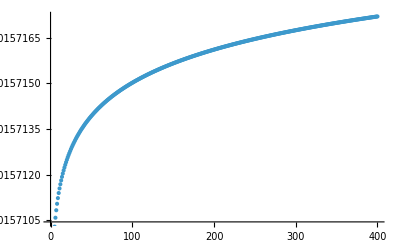

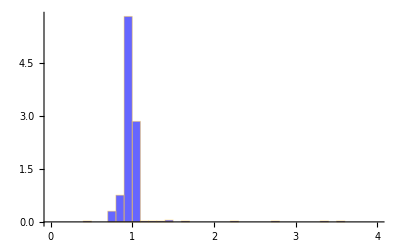

-Graphics-

```mathematica
ListPlot[OmegaQuantization]
Histogram[normalizedSpacings,{0,4,.1},"PDF",ChartStyle->{Opacity[0.6,Blue]}]
ListPlot[Transpose[{time,plot}],PlotStyle->{Blue,Thick},ScalingFunctions->{"Log","Log"}]
```

Sigma=2

```mathematica
OmegaQuantizationtwo={};
For[i=1, i<=1000, i++,
Value=Values[Quiet[FindRoot[Sin[alpha-beta]==Sin[2λ ω] /.λ->RandomVariate[NormalDistribution[-10^4,2/Sqrt[i]],1] /.l->i/.d->2,{ω,0.00015},WorkingPrecision->100]]];
	OmegaQuantizationtwo=Append[OmegaQuantizationtwo,Value[[1]]]
]
```

```mathematica
cumulativeDOS=Range[Length[OmegaQuantizationtwo]];
spline[x_]=Function[x,Fit[Transpose[{OmegaQuantizationtwo,cumulativeDOS}], Table[x^n,{n,0,4}],x]][x];
```

```mathematica
unfoldedE=spline[OmegaQuantizationtwo];

spacings=Differences[Sort[unfoldedE]];
```

```mathematica
meanSpacing=Mean[spacings];
normalizedSpacings=spacings/meanSpacing;
```

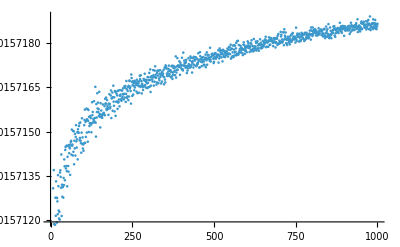

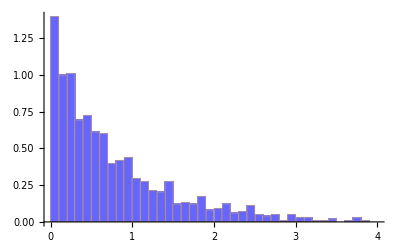

```mathematica
ListPlot[OmegaQuantizationtwo]
Histogram[normalizedSpacings,{0,4,.1},"PDF",ChartStyle->{Opacity[0.6,Blue]}]
```

```mathematica
SFF[t_]=Abs[Total[Exp[ⅈ*t*OmegaQuantizationtwo]]/1000000]^2;
plot=Array[SFF[#]&,1000000,{10^7,10^13}];
time=Array[#&,1000000,{10^7,10^13}];
```

```mathematica
ChartStyle->{Opacity[0.6,Blue]}
ListPlot[Transpose[{time,plot}],PlotStyle->{Blue,Thick},ScalingFunctions->{"Log","Log"}]
```

Sigma=0.025

```mathematica
OmegaQuantizationthree = {};
For[i=1, i<=400, i++,
	Value=Values[Quiet[FindRoot[Sin[alpha-beta]==Sin[2λ ω] /.λ->RandomVariate[NormalDistribution[-10^4,0.016/Sqrt[i]],1] /.l->i/.d->2,{ω,0.00015},WorkingPrecision->100]]];
	OmegaQuantizationthree=Append[OmegaQuantizationthree,Value[[1]]]
]
```

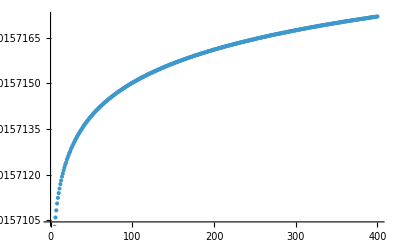

```mathematica
ListPlot[OmegaQuantizationthree]
```

```mathematica
cumulativeDOS=Range[Length[OmegaQuantizationthree]];
spline[x_]=Function[x,Fit[Transpose[{OmegaQuantizationthree,cumulativeDOS}], Table[x^n,{n,0,4}],x]][x];
```

```mathematica
unfoldedE=spline[OmegaQuantizationthree];
spacings=Differences[Sort[unfoldedE]];
```

```mathematica
meanSpacing=Mean[spacings];
normalizedSpacings25=spacings/meanSpacing;
```

```mathematica
histogram25=Histogram[normalizedSpacings25,{0,4,.1},"PDF",ChartStyle->{Opacity[0.6,Blue]}];
```

```mathematica
wignerDyson[x_]:=(32/Pi^2) x^2 Exp[-(4/Pi) x^2];
wdPlot=Plot[wignerDyson[x],{x,0,3},PlotStyle->{Blue,Thick}];
```

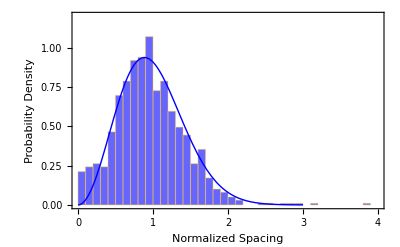

```mathematica
Show[histogram25,wdPlot,PlotRange->{{0,4},{0,1.2}},AxesOrigin->{0,0},Frame->True,FrameLabel->{"Normalized Spacing","Probability Density"},PlotLegends->{"Data","Wigner-Dyson"}]
```

```mathematica
SFF[t_]=Abs[Total[Exp[ⅈ*t*OmegaQuantizationthree]]/400]^2;
plot=Array[SFF[#]&,1000000,{10^7,10^13}];
time=Array[#&,1000000,{10^7,10^13}];
```

$Aborted

```mathematica
ListPlot[Transpose[{time,plot}],PlotStyle->{Blue,Thick},ScalingFunctions->{"Log","Log"},PlotRange->{10^(-7),1}]
```

-Graphics-

### Estimation of beta

```mathematica
p[s_, β_]=(1+α)Gamma[(2+β)/(1+α)]^(1+β)/Gamma[(1+β)/(1+α)]^(2+β)s^β Exp[-s^(α+1)Gamma[(2+β)/(1+α)]^(1+α)/Gamma[(1+β)/(1+α)]^(1+α)]
```

ⅇ^(-s^(1+α) Gamma[(1+β)/(1+α)]^(-1-α) Gamma[(2+β)/(1+α)]^(1+α)) s^β (1+α) Gamma[(1+β)/(1+α)]^(-2-β) Gamma[(2+β)/(1+α)]^(1+β)

```mathematica
cumulativebeta=0;
betas={};
For[n=1,n<=100,n++,
OmegaQuantizationBeta = {{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}}};
betaparameters = {{},{},{}};
For[k=2,k<=4,k++,
For[j=1,j<=10,j++,
For[i=1, i<=1000, i++,
	Value=Values[Quiet[FindRoot[Sin[alpha-beta]==Sin[2λ ω] /.λ->RandomVariate[NormalDistribution[-10^4,(0.01+0.001*j)/Sqrt[i]],1] /.l->i /. d->k,{ω,0.00015},WorkingPrecision->100]]];
	OmegaQuantizationBeta[[j]][[k-1]]=Append[OmegaQuantizationBeta[[j]][[k-1]],Value[[1]]];
];
cumulativeDOS=Range[Length[OmegaQuantizationBeta[[j]][[k-1]]]];
spline[x_]=Function[x,Fit[Transpose[{OmegaQuantizationBeta[[j]][[k-1]],cumulativeDOS}], Table[x^n,{n,0,4}],x]][x];

unfoldedE=spline[OmegaQuantizationBeta[[j]][[k-1]]];
spacings=Differences[Sort[unfoldedE]];

meanSpacing=Mean[spacings];
normalizedSpacings=spacings/meanSpacing;

{binEdges, binCounts}=HistogramList[normalizedSpacings,{0,4,.1},"PDF"];
binMidpoints = (binEdges[[1 ;; -2]] + binEdges[[2 ;; -1]]/2);
fit = NonlinearModelFit[Transpose[{binMidpoints, binCounts}],p[s, β]/.α->1,β,s];
betaparameters[[k-1]] = Append[betaparameters[[k-1]],Values[fit["BestFitParameters"]][[1]]];
(*Show[Histogram[normalizedSpacings,{0,4,.1},"PDF",ChartStyle->{Opacity[0.6,Blue]}],Plot[p[x,betaparameters[[k-1]][[j]]]/.α->1,{x,0,3},PlotStyle->{Blue,Thick}],PlotRange->{{0,4},{0,1.2}},AxesOrigin->{0,0},Frame->True,FrameLabel->{"Normalized Spacing","Probability Density"},PlotLegends->{"Data","Wigner-Dyson"}]*)
]
];
betas=AppendTo[betas,betaparameters];
cumulativebeta = cumulativebeta +betaparameters;
]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

{{{1.93364,1.60681,1.96145,1.55496,1.27071,1.53164,1.00765,0.69805,0.827115,0.670679},{1.83776,1.71179,1.36637,1.34105,1.25674,0.892241,0.966192,0.833474,0.845513,0.641481},{1.63046,1.39771,1.59783,1.05154,1.16736,0.913711,0.820805,0.776095,0.713616,0.748073}},{{1.98867,1.83368,1.64047,1.22205,1.33108,1.19459,0.894073,0.662005,0.888774,0.696951},{1.7602,1.52781,1.46416,1.31449,1.16762,0.803315,0.877907,0.843722,0.509396,0.689726},{1.84292,1.70505,1.43618,1.32482,1.10561,0.94708,1.03608,0.669246,0.870087,0.721048}},{{1.74449,1.81591,1.62794,1.43296,1.36585,0.940812,0.943776,0.761445,0.658108,0.763527},{1.90172,1.57439,1.40425,1.14922,1.23757,1.14722,0.904865,0.781453,0.678281,0.649512},{1.91735,1.49498,1.51344,1.10863,1.02364,0.983441,0.920565,0.889691,0.539798,0.613337}},{{1.99329,2.02904,1.84346,1.49255,1.11602,1.40209,1.16954,0.972363,0.615463,0.774596},{2.1549,1.83817,1.69819,1.43305,1.18327,0.939377,0.823592,0.879746,0.746884,0.635521},{1.877,1.59225,1.54206,1.21003,0.886384,1.00216,0.839506,0.876327,0.705541,0.519546}},{{1.93984,1.65986,1.6674,1.40396,1.133,1.17472,1.08193,0.798606,0.576802,0.892562},{1.91355,1.76365,1.5341,1.32511,1.11699,0.978467,0.964744,0.613433,0.707565,0.543277},{1.88843,1.54412,1.67161,1.06168,1.06217,1.02088,0.935067,0.584873,0.804471,0.643679}},{{1.71924,1.64428,1.78374,1.5177,1.17648,1.04538,0.799463,0.630948,0.763242,0.544573},{1.86711,1.73086,1.65227,1.43219,1.07241,0.894002,0.931508,0.649281,0.794357,0.524788},{1.49053,1.42501,1.68087,1.32535,1.18813,1.23225,0.616693,1.10855,0.820613,0.588956}},{{1.99642,1.73585,1.64899,1.55896,1.43106,1.14643,0.968194,0.800702,0.624724,0.387179},{1.9336,1.67137,1.53146,1.31631,1.07721,0.721156,0.774456,0.882485,0.759544,0.593629},{1.64304,1.84375,1.42727,1.18053,1.15978,0.923636,0.991838,0.830538,0.504878,0.628462}},{{1.89888,1.65962,1.51836,1.2625,1.21051,1.29806,0.905693,0.804272,0.660298,0.551461},{1.77648,1.68941,1.3808,1.25471,1.19371,1.24512,1.03637,0.894077,0.58405,0.68598},{1.79397,1.50206,1.5768,1.10477,1.53079,1.04665,0.85207,0.727986,0.541947,0.650961}},{{1.75426,1.81666,1.49326,1.55362,1.3671,0.880108,0.850009,0.879793,0.76552,0.554432},{1.92762,1.67655,1.32612,1.42352,1.05682,1.25948,1.00602,0.972702,0.721314,0.51005},{1.95887,1.46892,1.42245,1.28934,1.21006,0.848051,0.936258,0.681502,0.567045,0.715976}},{{1.87848,1.71632,1.54531,1.35785,1.15921,0.972453,0.858699,0.719898,0.806039,0.800365},{1.8335,1.58479,1.49572,1.38723,1.23119,1.15269,0.986682,0.728109,0.609241,0.456195},{1.86338,1.65744,1.36992,1.40672,1.11352,0.970556,0.714579,0.890215,0.741614,0.653927}},{{1.68915,1.63299,1.55547,1.40115,1.14157,0.996685,0.878158,0.909609,0.829921,0.685654},{1.6579,1.6703,1.48292,1.33153,1.10612,0.929402,0.937051,0.780419,0.585247,0.609601},{1.6708,1.67793,1.37636,1.22187,0.950781,1.16097,0.730335,0.822742,0.611561,0.563722}},{{1.8473,1.89268,1.40589,1.30606,1.53825,1.15155,0.978176,0.88554,0.699925,0.831748},{1.63471,1.44591,1.51659,1.31424,1.24627,0.969449,0.991859,0.871417,0.750782,0.679743},{1.66397,1.71669,1.36654,1.30128,1.09567,1.07097,0.905768,0.766771,0.85436,0.656277}},{{1.83633,1.847,1.48467,1.1159,1.35193,0.947322,0.938103,0.673644,0.756303,0.710153},{1.97733,1.74903,1.5465,1.45286,1.13111,1.10473,0.623103,0.997908,0.726261,0.505715},{1.78853,1.40196,1.25297,1.21037,1.04741,0.999437,0.813127,0.8708,0.691507,0.558741}},{{1.54141,1.50318,1.49999,1.12609,1.20418,1.10197,0.767384,0.846076,0.704124,0.665555},{1.78012,1.78147,1.64918,1.27751,1.25778,0.939832,0.886857,0.788663,0.737933,0.381279},{1.6388,1.64695,1.72735,1.28779,1.03691,1.04216,0.856074,0.768676,0.523098,0.59414}},{{1.78859,1.67274,1.48335,1.14759,1.34053,0.965012,1.09617,0.678245,0.955464,0.807469},{1.78091,1.81838,1.53192,1.12235,1.02345,0.967033,1.11597,0.776044,0.763253,0.494668},{1.73278,1.70036,1.3272,1.30564,1.18153,1.01792,0.971669,0.837268,0.630098,0.594163}},{{1.78458,1.75739,1.58774,1.4784,1.35403,1.15343,1.00442,0.560892,0.716761,0.499198},{1.96454,1.65031,1.42805,1.45215,1.74375,1.11853,0.783758,0.740056,0.501326,0.668067},{1.7869,1.74534,1.47567,1.2542,1.05612,1.12535,0.95268,0.718715,0.75806,0.742004}},{{1.98616,1.51917,1.44974,1.3318,1.2114,0.862753,0.786967,0.681811,0.882628,0.65379},{1.8596,1.68527,1.51443,1.28049,1.18444,1.20687,0.883676,0.741252,0.784536,0.762373},{1.64443,1.35281,1.57608,1.09238,1.0877,1.20661,0.720546,0.676232,0.727728,0.697185}},{{1.84943,1.57875,1.5887,1.26614,1.11824,1.06821,1.0358,0.835765,0.910783,0.65886},{1.91267,1.61488,1.27697,1.22775,1.24606,0.861372,0.906247,0.664476,0.758803,0.761705},{1.71343,1.39828,1.41744,1.08153,1.39507,0.900696,1.03408,0.813758,0.734567,0.605197}},{{1.83537,1.63885,1.43486,1.0928,1.3576,1.05194,0.897472,0.550857,0.711099,0.770149},{2.0136,1.67696,1.74206,1.37071,1.32259,0.891282,0.762651,0.74433,0.699604,0.545917},{1.91746,1.6191,1.41498,1.0045,1.17398,1.05123,0.936488,0.609244,0.907931,0.442351}},{{1.88449,1.56768,1.55264,1.4175,1.39689,1.00462,0.967959,0.881573,0.842417,0.614949},{1.80087,1.70114,1.55544,1.12996,1.05832,1.20156,0.863969,0.776205,0.818669,0.690165},{1.90927,1.62632,1.50646,1.34004,1.00764,0.900416,0.867373,0.78977,0.707551,0.591641}},{{1.86561,1.5784,1.56258,1.54093,1.34047,1.18872,1.03426,0.862658,0.531332,0.841395},{1.85384,1.69512,1.53597,1.42686,1.36612,1.05625,0.861243,0.753405,0.847554,0.508664},{1.63735,1.85833,1.36192,1.23051,1.00539,0.882646,0.973791,0.793107,0.662112,0.629589}},{{2.12765,1.4606,1.71551,1.26928,1.25124,1.0688,1.01206,0.881099,0.772736,0.599511},{1.56589,1.50737,1.53863,1.58951,1.54638,0.948884,0.786921,0.714686,0.579565,0.63234},{1.71399,1.37788,1.48057,1.20902,1.01551,1.07016,0.869728,0.915823,0.768136,0.572128}},{{1.87422,1.75208,1.62154,1.36593,1.26557,1.20813,1.03771,0.821431,0.854241,0.809924},{1.8067,1.63868,1.33353,1.10104,1.1509,1.16758,0.988634,0.743764,0.583945,0.733203},{1.78946,1.61369,1.26863,1.10955,1.19653,0.951791,0.909569,0.728722,0.78688,0.633451}},{{1.64415,1.75816,1.59892,1.41656,1.13487,0.877653,0.931347,0.959021,0.628756,0.611395},{1.64922,1.73336,1.3483,1.23802,1.19036,1.07755,0.94781,0.923026,0.785578,0.535228},{1.80146,1.92586,1.31779,1.25987,1.16664,1.33727,0.598139,0.963471,0.967787,0.595235}},{{1.99757,1.63848,1.5019,1.50268,1.27352,0.871784,0.910592,0.978122,0.880181,0.734847},{1.84051,1.7424,1.73892,1.41421,1.39774,0.922426,1.01351,0.690106,0.649612,0.608054},{1.8004,1.54614,1.27227,1.36605,1.26626,1.01099,0.945166,0.720496,0.776011,0.726823}},{{1.8589,1.45837,1.72631,1.54916,1.20135,1.01239,1.07921,0.995285,0.586424,0.521228},{1.65552,1.57213,1.50848,1.365,1.04147,1.00459,0.828463,1.00434,0.670342,0.601195},{1.58767,1.72124,1.27045,1.46469,1.24171,1.01494,0.794705,0.869857,0.820535,0.831933}},{{1.89731,1.97534,1.79728,1.26542,0.945364,1.03625,0.841222,0.740825,0.736651,0.69759},{1.88569,1.58151,1.27209,1.3906,1.00856,1.04426,0.777977,0.706779,0.665713,0.660154},{1.76221,1.68463,1.38694,1.23741,1.27346,0.814348,0.828129,0.753112,0.651905,0.593726}},{{1.91745,1.88456,1.60431,1.30793,1.32335,1.05511,1.16201,0.828004,0.568988,0.612207},{1.84396,1.75914,1.56312,1.34712,1.01939,0.976591,0.903572,0.752798,0.818169,0.639172},{1.67076,1.41869,1.35894,1.24,1.07738,0.933936,0.963633,0.588992,0.632298,0.767379}},{{1.74521,1.70866,1.28539,1.29692,1.03445,1.1673,0.859412,0.961343,0.801413,0.599227},{1.98729,1.74801,1.33168,1.20252,1.1924,0.902263,0.850475,0.960004,0.686521,0.693504},{1.88581,1.58454,1.51867,1.16859,0.962239,0.841297,1.22759,0.746809,0.653749,0.572683}},{{1.68773,1.63821,1.34088,1.38851,1.12545,1.16336,0.788116,0.751519,0.604422,0.61593},{1.83838,1.86949,1.45102,1.28349,1.16511,0.941569,0.928044,0.731828,0.657229,0.759979},{1.73903,1.43057,1.40626,1.30727,1.03689,1.08129,0.913839,0.837331,0.586052,0.643774}},{{1.81411,1.70449,1.5503,1.43563,0.984837,1.01719,0.976362,1.17552,0.770962,0.595537},{1.68123,1.55921,1.53587,1.41084,1.21603,0.978753,0.768463,1.03694,0.659137,0.724544},{1.68113,1.75427,1.43666,1.29671,1.26684,0.859993,0.813761,0.715837,0.760061,0.911582}},{{1.91641,1.65629,1.65101,1.45389,1.34638,1.13925,1.21208,0.76131,0.586435,0.477625},{1.94108,1.63644,1.37131,1.33168,1.14395,0.975941,1.05307,0.597674,0.978299,0.585347},{1.66039,1.60309,1.55961,1.2441,0.907856,1.29169,0.615063,0.761021,0.472926,0.638155}},{{1.78401,1.50787,1.50613,1.55559,1.04917,1.17464,1.15843,0.730323,0.713186,0.699412},{1.88412,1.58757,1.60923,1.48896,1.053,1.1312,1.06709,0.748688,0.764791,0.571983},{1.54056,1.81494,1.26943,1.45406,1.04604,1.02312,0.98809,0.66185,0.86305,0.669274}},{{2.00157,1.53463,1.56252,1.42186,1.09334,1.06751,1.27776,0.864871,0.727558,0.68913},{1.83872,1.62494,1.48874,1.2695,1.25858,0.876989,0.757871,0.995755,0.75146,0.675585},{1.76882,1.62117,1.62279,1.2038,1.06152,1.03551,1.04043,0.959719,0.538654,0.529406}},{{2.23926,1.77384,1.52094,1.2321,1.16093,1.29469,0.943268,0.808319,0.823568,0.641312},{1.63194,1.65995,1.36633,1.1054,1.28569,0.745269,0.870412,0.62412,0.64304,0.67118},{1.71596,1.71817,1.4055,1.39432,1.26004,1.11325,1.08072,0.683272,0.854981,0.564029}},{{1.89949,1.58798,1.29445,1.5927,1.34422,1.10515,0.849864,0.889057,0.939949,0.857155},{1.72264,1.73738,1.30205,1.18538,1.16698,1.05686,1.00451,0.781562,0.646733,0.589299},{1.8822,1.68043,1.46698,1.30223,1.2859,0.974717,0.905719,0.974023,0.834575,0.653259}},{{1.82734,1.72669,1.39803,1.32472,1.38128,1.18936,0.997223,0.831402,0.754577,0.603301},{1.80709,2.05151,1.57683,1.2932,1.04737,1.14944,1.13376,0.96319,0.5973,0.631192},{1.68171,1.43854,1.5681,1.48394,1.04483,1.00719,0.726287,0.915995,0.727873,0.593551}},{{1.83778,1.91583,1.52258,1.27731,1.37947,1.00882,0.687466,0.765772,0.820427,0.718006},{1.86986,1.81353,1.54033,1.25637,0.932663,1.21534,1.01657,0.761705,0.572144,0.668811},{1.44593,1.58618,1.38319,1.11582,1.17174,0.838081,1.09126,0.70903,0.70974,0.491032}},{{1.85267,1.61344,1.51679,1.3895,1.15145,1.11333,0.778561,0.80549,0.832491,0.598787},{1.84557,1.4022,1.52033,1.47421,1.16061,1.08923,0.950522,0.840594,0.79072,0.614511},{1.92512,1.52688,1.25847,1.42347,1.17881,1.05015,1.24548,0.769723,0.825795,0.696629}},{{2.07609,1.78613,1.47047,1.08899,1.28068,1.14641,0.819518,0.714024,0.747162,0.618314},{1.9039,1.52548,1.57926,1.73437,1.37907,1.36444,0.718866,0.847645,0.822878,0.36954},{1.52855,1.5263,1.44873,1.27431,1.19446,1.12206,0.90134,0.784719,0.74523,0.497445}},{{1.86901,1.74403,1.85904,1.35102,1.2084,0.960535,0.87952,0.745244,0.602037,0.589101},{1.92885,1.59408,1.69453,1.14545,1.2408,1.23508,0.863009,0.793002,0.882031,0.528418},{1.57695,1.86325,1.43263,1.27466,1.40963,1.23562,0.714041,0.698208,0.527205,0.574836}},{{1.76973,1.78724,1.5228,1.31205,1.05582,1.11886,0.947127,0.778095,0.843286,0.718472},{1.76285,1.77304,1.4622,1.17944,1.20193,1.10223,0.814511,0.988965,0.79893,0.558868},{1.86105,1.58537,1.46247,1.44106,1.25494,1.21338,0.849263,0.766088,0.573896,0.60536}},{{1.84909,1.60906,1.90109,1.66138,1.2572,1.20041,0.838458,0.742469,0.602412,0.924324},{1.6755,1.79851,1.55624,1.35574,1.07702,0.922605,0.774395,0.772668,0.681082,0.532361},{1.81975,1.7516,1.4611,1.42759,1.457,1.0468,0.925919,0.594754,0.661757,0.510083}},{{1.79266,1.86037,1.35849,1.56629,1.36753,1.21463,0.939148,0.824239,0.784834,0.831917},{1.92087,1.7601,1.39149,1.24347,1.41673,0.697464,0.852263,0.846027,0.680899,0.457713},{1.59536,1.66805,1.33512,1.4777,1.1861,1.06812,0.848601,1.04507,0.663961,0.479007}},{{2.13513,1.52754,1.68044,1.77592,1.24686,1.35865,1.18176,0.795373,0.746681,0.600094},{1.69414,1.60558,1.49805,1.48906,1.15563,0.811503,0.920846,0.635468,0.762139,0.680523},{1.87243,1.75162,1.92554,1.24049,1.07552,1.0029,1.02283,0.644418,0.678887,0.877543}},{{2.07459,1.62284,1.63043,1.40661,1.03546,1.04747,1.01273,0.786087,0.63548,0.899013},{1.75344,1.43577,1.55287,1.43335,1.10698,0.862513,0.877746,0.772032,0.698959,0.446428},{1.7686,1.47755,1.35089,1.22759,1.12576,0.99498,0.764654,0.88809,0.768101,0.679958}},{{1.84655,1.61487,1.73987,1.43136,1.2595,1.23462,1.10647,1.00788,0.70001,0.767019},{1.78402,1.63736,1.54814,1.29134,1.05635,1.11632,1.0289,1.00149,0.598128,0.499767},{1.91931,1.61541,1.53338,1.5803,1.08058,1.06255,0.665693,0.851076,0.792427,0.591521}},{{1.94559,1.5494,1.43062,1.3566,1.04666,1.11185,1.1289,1.01715,0.694881,0.555768},{1.84752,1.78372,1.48995,1.22742,1.33761,0.928533,0.68335,0.932344,0.78279,0.613186},{1.50793,1.60737,1.45895,1.16484,1.27818,1.07055,0.857622,0.695185,0.677202,0.561438}},{{2.09673,2.07025,1.41583,1.24607,1.30937,1.36878,0.908697,0.930796,0.681516,0.793144},{1.85802,1.85227,1.54715,1.30771,1.22591,0.964937,0.850183,0.614595,0.707319,0.632656},{1.67173,1.48695,1.45276,1.44086,1.17486,1.05414,1.29196,0.556153,0.648491,0.683114}},{{1.96701,1.68565,1.66781,1.50414,1.14807,1.01133,0.974037,1.1221,0.968203,0.609202},{1.68815,1.69203,1.314,1.41432,1.12631,0.99568,1.1363,0.741161,0.828949,0.643003},{1.90139,1.64474,1.49212,1.34798,1.15418,0.736453,0.968299,0.717931,0.664788,0.62083}},{{1.91358,1.78936,1.25835,1.43018,1.44566,0.928069,0.872491,1.07488,0.700951,0.614662},{1.7597,1.83156,1.57232,1.342,0.986714,1.1087,0.759594,0.916774,0.705941,0.647801},{1.82871,1.62645,1.51616,1.35634,1.20265,1.26738,0.875131,0.946422,0.594599,0.745796}},{{1.88594,1.72346,1.58265,1.44254,1.13925,1.03432,0.989905,0.970913,0.604819,0.735862},{1.82937,1.55287,1.61727,1.33692,1.24555,1.30759,0.827826,0.875616,0.738318,0.86104},{1.96142,1.44202,1.72609,1.32154,1.27823,0.950318,0.970831,0.934502,0.680379,0.507892}},{{2.14062,1.71812,1.82471,1.37577,1.25545,1.08172,0.830775,1.04641,0.817867,0.656668},{1.94826,1.67632,1.46824,1.38044,1.22092,0.97313,0.848102,0.847146,0.666836,0.581385},{1.80791,1.65726,1.27973,1.33637,1.11699,0.923411,0.582986,0.675354,0.681515,0.583389}},{{1.92392,1.79719,1.45306,1.3335,1.3781,1.1027,0.907734,0.753655,0.539545,0.612892},{2.04409,1.62539,1.19571,1.42764,1.23353,0.948516,0.929994,0.999053,0.493887,0.725169},{1.80755,1.48904,1.49893,1.25198,1.08801,1.21321,0.87608,0.812054,0.672915,0.626713}},{{2.00389,1.66203,1.42306,1.5946,1.53569,1.32518,0.944369,0.724701,0.79925,0.49713},{1.7668,1.66002,1.60723,1.495,1.50318,1.02019,1.11941,0.877485,0.661188,0.66939},{1.92622,1.52388,1.38416,1.28597,0.979182,1.07437,0.853537,0.789453,0.751471,0.635781}},{{1.9169,1.49317,1.64889,1.463,1.25189,0.839514,1.02705,1.20728,0.569293,0.634639},{2.0296,1.573,1.49633,1.34046,1.12457,0.982117,0.950576,0.626347,0.788097,0.466339},{1.82848,1.6765,1.55512,1.31058,1.20409,1.1244,0.660988,1.01388,0.672238,0.733533}},{{2.27195,1.75539,1.78238,1.65893,1.33543,1.00393,1.09886,0.665321,0.772242,0.579953},{2.1465,1.56316,1.25664,1.21085,1.14337,0.905932,1.06995,0.845634,0.91503,0.661043},{1.82364,1.45042,1.42173,1.21821,1.03536,1.08664,0.799279,0.709698,0.745477,0.630564}},{{2.24633,1.55416,1.63396,1.38255,1.05142,1.10573,0.857104,0.800955,0.615508,0.538145},{1.79109,1.97891,1.30275,1.63008,0.987766,1.03912,0.901906,0.749475,0.81394,0.579527},{1.6359,1.63665,1.52623,1.15271,1.04297,0.9321,0.830237,0.54453,0.798563,0.591296}},{{1.90419,1.42519,1.23436,1.3078,1.16077,0.996393,0.881565,0.80766,0.765622,0.811052},{1.98471,1.97239,1.42883,1.43291,1.05973,0.917907,0.960988,0.773312,0.693908,0.730903},{1.64325,1.63878,1.60088,1.16183,1.12913,1.19647,0.840679,0.713196,0.680927,0.448877}},{{2.23386,1.92785,1.83086,1.41613,1.3985,0.986868,0.883762,0.847928,0.585388,0.562423},{1.72582,1.55215,1.4215,1.4502,1.32909,1.01534,1.09634,0.787313,0.558516,0.712066},{1.81566,1.55388,1.37575,1.21639,1.12967,0.879486,0.720531,0.762533,0.753985,0.685836}},{{1.70955,1.791,1.46578,1.33949,1.40142,1.10743,1.14262,0.794485,0.764922,0.867468},{1.75043,1.69503,1.67017,1.7183,1.08819,1.04285,0.96103,0.802967,0.590489,0.651888},{1.71938,1.93582,1.35921,1.24381,1.16637,0.950511,0.898742,0.697968,0.85108,0.574568}},{{2.06517,1.51967,1.46528,1.53403,1.22786,1.21899,1.15211,1.06508,0.563692,0.714568},{1.75168,1.77316,1.55983,1.48993,1.20398,1.27035,1.02451,0.837281,0.634984,0.479642},{1.62812,1.8097,1.50734,1.34939,1.01314,0.878023,0.72193,0.807951,0.764882,0.779094}},{{1.90236,1.87582,1.55069,1.21741,1.11414,1.04833,1.02484,1.08511,0.78543,0.650504},{1.90485,1.49503,1.58728,1.43374,1.1187,1.01483,1.01676,0.844507,0.854696,0.672234},{1.97056,1.42521,1.47482,1.26017,1.07547,0.881707,0.848583,0.822686,0.845668,0.481836}},{{1.92311,1.65933,1.58056,1.48635,1.66804,1.04805,1.01683,0.868543,0.615745,0.771971},{1.81615,1.69816,1.60325,1.21517,0.962035,0.926439,1.04901,0.889068,0.761353,0.649381},{1.46592,1.67627,1.50642,1.09102,1.04889,1.00808,1.04219,0.891507,0.533656,0.573418}},{{1.79372,1.75268,1.61903,1.18974,1.15168,0.669624,0.625188,1.01408,0.797804,0.448945},{1.61351,1.58943,1.30797,1.66109,1.27795,0.895815,1.0595,0.718705,0.748182,0.627312},{1.52197,1.50974,1.19725,1.3407,1.39237,1.01033,0.986051,0.813874,0.869632,0.53404}},{{1.7702,1.56614,1.56562,1.44622,1.16194,0.959471,1.0227,0.630635,0.705911,0.680952},{1.85581,1.8139,1.76917,1.21213,1.26696,1.00649,0.99339,0.734951,0.884658,0.651615},{2.16374,1.62031,1.27906,1.26066,1.02562,0.902837,1.09328,0.698105,0.738399,0.648708}},{{1.9885,1.73387,1.56966,1.40761,1.44226,1.23448,0.84347,0.714563,0.604663,0.763032},{1.69373,1.66766,1.66338,1.40945,1.23825,1.20831,0.694174,0.787568,0.844745,0.563077},{1.52453,1.74595,1.23861,1.19673,1.089,0.870879,0.935083,0.945544,0.706946,0.598701}},{{1.92718,1.86844,1.50788,1.30697,1.19136,0.912955,0.900607,0.87889,0.812099,0.675798},{1.72269,1.72006,1.47934,1.48421,1.1479,1.07161,0.83453,0.975094,1.09607,0.657532},{1.86433,1.39064,1.49585,1.23306,1.12787,1.15818,0.89244,0.630744,0.793081,0.600625}},{{2.23628,1.73283,1.53851,1.569,1.06436,1.40792,0.858726,0.844182,0.7486,0.715356},{1.95855,1.70865,1.58745,1.52657,1.16327,1.07573,0.939219,0.931375,0.722174,0.605794},{1.703,1.46703,1.59359,1.34339,0.974264,0.930362,0.817797,0.950829,0.587377,0.651682}},{{1.80115,1.72698,1.50117,1.38671,1.19592,1.08145,0.87505,0.758483,0.498118,0.643145},{1.82222,1.69272,1.57274,1.35306,1.22035,1.0037,1.00235,0.91679,0.690373,0.557119},{1.89386,1.66854,1.62116,1.40635,1.15011,1.0069,0.870347,0.817875,0.683464,0.578748}},{{1.82033,1.49589,1.58458,1.23157,1.51827,1.04479,1.055,0.854288,0.998157,0.668852},{1.60045,1.80121,1.37618,1.36195,1.04263,1.24893,0.84081,1.05792,0.560809,0.55851},{1.84093,1.55663,1.3542,1.24284,1.22777,0.934311,0.797185,0.810563,0.734693,0.652202}},{{1.64328,1.70695,1.57245,1.1194,1.19165,1.10724,0.917763,1.02385,0.694462,0.671093},{1.60636,1.59294,1.73111,1.35705,1.28637,0.952795,0.832852,0.914643,0.697292,0.613748},{1.82775,1.75999,1.36438,1.47718,1.34501,0.826699,0.764399,0.752679,0.714067,0.500306}},{{1.7606,1.81443,1.63022,1.6094,1.11851,1.13008,1.10982,0.869088,0.603881,0.633284},{1.84532,1.7256,1.36039,1.23195,0.820356,0.789566,0.868254,0.680934,0.738301,0.620439},{1.67148,1.60344,1.35226,1.11833,1.42067,0.919924,0.875728,0.890947,0.568734,0.68475}},{{1.943,1.59283,1.67949,1.61813,1.36871,1.19462,0.924765,1.00712,0.664646,0.482221},{1.81051,1.80749,1.69948,1.19513,1.18827,1.10355,0.857456,0.728046,0.569729,0.719878},{1.98131,1.61498,1.59396,1.21111,0.922555,1.06631,0.886532,0.866957,0.673836,0.46313}},{{2.1181,1.77173,1.53605,1.50947,1.33841,1.08487,1.63332,0.73049,0.645875,1.10259},{1.81466,1.73647,1.48809,1.47151,1.11076,0.965114,1.09136,0.935606,0.775858,0.382506},{1.60068,1.5924,1.5543,1.23763,1.22652,1.35237,0.819828,0.868309,0.818519,0.402651}},{{2.08789,1.52852,1.68345,1.35135,1.27366,1.14628,0.957128,0.834785,0.768478,0.639318},{1.92771,1.56633,1.45386,1.26209,1.19213,0.764062,0.958869,0.592838,0.754421,0.645624},{1.77727,1.67433,1.46781,1.17271,1.15334,0.969836,0.849364,0.697599,0.568814,0.629609}},{{2.01763,1.88821,1.70702,1.54443,1.03828,1.27654,0.883404,0.731917,0.681394,0.632624},{1.71469,1.58028,1.70574,1.4025,1.09602,1.13982,0.786107,0.931198,0.937916,0.723761},{1.50627,1.48981,1.35839,1.22402,0.979383,1.11076,0.759923,0.654005,0.787362,0.575534}},{{1.70939,1.57295,1.556,1.79456,1.05912,1.13195,0.87271,0.828115,0.696862,0.64671},{1.83207,1.76694,1.61462,1.23258,1.32329,0.949818,0.968523,0.746089,0.661292,0.619985},{1.8377,1.66609,1.34896,1.15224,1.16702,1.12439,0.846175,0.897498,0.7105,0.505699}},{{1.88,1.52106,1.68368,1.57273,1.07672,0.999426,0.9108,0.896999,0.892844,0.696749},{1.77477,1.52448,1.49023,1.39154,1.25043,0.836606,0.840174,0.94199,0.798644,0.533942},{1.98319,1.47847,1.67506,1.39854,1.10896,1.01049,0.77246,0.614926,0.686495,0.769692}},{{1.91371,1.61016,1.77716,1.40135,1.02058,1.0501,1.03217,0.807742,0.844464,0.496053},{2.15028,2.0704,1.21295,1.08974,1.1557,1.1845,0.804955,0.937858,0.676015,0.771006},{1.76547,1.5882,1.35359,1.28072,1.22669,1.3842,0.707343,1.03074,0.569103,0.556917}},{{1.9341,1.66844,1.70667,1.37083,1.37665,0.881392,0.907813,0.795647,0.839612,0.555123},{1.75561,1.6688,1.49323,1.23429,1.24889,1.19241,1.08157,1.03273,0.78354,0.648035},{1.90064,1.51375,1.62145,1.09346,1.18598,1.2501,0.925597,0.633264,0.602418,0.787727}},{{2.20483,1.76245,1.43013,1.45855,1.14678,0.977773,0.795808,0.757668,0.688414,0.512774},{1.73698,1.85082,1.65058,1.45172,1.52437,1.02942,0.684063,0.758666,0.526686,0.494539},{1.6306,1.63212,1.28197,1.3183,1.23049,1.06682,1.00347,0.529394,0.64174,0.617263}},{{1.76072,1.65254,1.64397,1.31246,1.2668,1.28002,0.810159,0.829191,0.710244,0.778972},{1.70289,1.71396,1.75709,1.69352,1.22378,1.05814,1.18824,0.72553,0.996698,0.398043},{1.82897,1.82353,1.5491,1.3812,0.959495,1.03305,0.835356,0.782249,0.634417,0.606617}},{{1.81785,1.87248,1.58625,1.21171,1.12578,1.38645,0.868282,0.963737,0.695022,0.645996},{1.62945,1.64945,1.53733,1.62606,1.02943,0.976899,0.956592,0.774371,0.659687,0.702759},{1.75014,1.67119,1.51116,1.33707,1.08765,0.97383,0.957663,0.807295,0.852737,0.560656}},{{1.79384,1.85507,1.58058,1.23235,1.28332,0.964924,1.19611,1.12622,0.945201,0.644779},{1.89283,1.57442,1.45236,1.30123,1.35163,1.01449,0.854424,0.64783,0.503702,0.863838},{1.67405,1.54637,1.5357,1.7759,1.29813,1.18001,0.821476,0.754201,0.836616,0.781966}},{{1.93973,1.84866,1.7444,1.24029,1.26191,1.16076,0.833304,0.691663,0.708686,0.590328},{1.73056,1.81534,1.57986,1.32432,1.17514,1.0389,0.861311,0.89501,0.569314,0.641633},{1.66634,1.42274,1.61648,1.26475,1.01473,1.16323,0.897037,0.760577,0.912203,0.579479}},{{1.73165,1.76338,1.44888,1.2866,1.25216,1.12517,1.10705,0.792106,0.985131,0.708427},{1.93766,1.76281,1.51294,1.19265,1.21423,0.882353,0.94345,0.62944,0.736256,0.609801},{1.5605,1.61104,1.61678,1.44561,1.19393,0.930382,0.838274,0.756699,0.511728,0.589459}},{{1.67172,1.58038,1.59471,1.66299,1.17629,1.07464,0.853749,0.774481,0.777403,0.477572},{1.8172,1.82884,1.37761,1.40453,1.13121,1.16927,1.06729,0.772077,0.762349,0.621089},{1.59025,1.54993,1.67262,1.33318,1.13624,1.13185,0.875255,0.645654,0.830396,0.69441}},{{1.82778,1.73981,1.61968,1.45018,1.32489,1.34975,0.873433,0.942074,0.914336,0.561874},{1.86244,1.58028,1.39671,1.61392,1.42771,1.16722,0.858253,0.726353,0.559969,0.659494},{1.81309,1.41696,1.51682,1.33068,1.18935,1.06437,0.802289,0.823427,0.719419,0.490333}},{{2.08808,1.54514,1.5766,1.28272,0.962113,1.18562,1.08154,0.787034,0.699304,0.650606},{1.93788,1.36768,1.41729,1.32429,1.10505,1.05085,1.02855,1.00441,0.59414,0.856616},{1.87636,1.57447,1.36426,1.15928,1.11921,1.11732,1.12419,0.660991,0.48108,0.952728}},{{2.0467,2.00125,1.81697,1.3208,1.32593,0.894708,1.04277,1.03844,0.746227,0.625213},{1.85483,1.71706,1.43894,1.04127,1.04845,0.976161,0.91897,0.93794,0.611243,0.804981},{1.62583,1.32907,1.39645,1.46378,0.961637,0.894023,0.947251,0.688027,0.726917,0.713391}},{{1.80628,1.6221,1.62006,1.44416,1.07329,1.03203,1.25626,1.17946,0.828197,0.863696},{1.82392,1.77524,1.32778,1.33982,1.22303,1.01987,1.03305,0.683701,0.703629,0.774155},{2.05947,1.66096,1.39696,1.3198,1.36379,1.02533,1.09315,0.78788,0.857853,0.514977}},{{1.9253,1.52867,1.52758,1.31846,1.35721,1.00939,0.805751,1.04922,0.782902,0.679651},{1.92106,1.95358,1.57991,1.36239,1.18755,0.824982,0.992556,0.814426,0.665855,0.652857},{1.39463,1.43928,1.41349,1.16261,1.13609,1.14055,0.816616,0.767353,0.752932,0.723314}},{{2.02011,1.70898,1.78062,1.32236,1.38566,1.14708,0.89871,0.830453,0.435151,0.837515},{1.93453,1.62036,1.33358,1.53716,1.23696,1.1308,0.936402,0.853782,0.511003,0.525647},{1.76637,1.54375,1.44687,1.44782,1.39932,0.992305,0.827512,0.774592,0.716886,0.570245}},{{1.98476,1.72097,1.55179,1.36774,1.18037,1.12323,1.02992,0.807494,0.542993,0.550925},{1.73707,1.82821,1.27003,1.62672,1.45278,1.17713,0.813674,0.910937,0.960458,0.59827},{1.93149,1.82208,1.37169,1.14425,1.18828,1.32594,0.993203,0.755837,0.684628,0.564134}},{{1.91256,1.90181,1.43955,1.52275,1.29974,1.06962,1.01261,0.844849,0.734277,0.738744},{1.64043,1.55635,1.40916,1.43423,0.940084,1.12688,0.846567,0.878582,0.557062,0.552703},{1.67043,1.8609,1.35164,1.2706,1.43414,1.05866,0.998831,0.790448,0.61789,0.551765}},{{1.76058,1.70877,1.85758,1.37398,1.00113,0.88091,1.0032,0.691098,0.65735,0.567395},{1.68274,1.69885,1.49102,1.39504,1.35605,0.862347,0.92142,0.908658,0.610347,0.538263},{1.77406,1.74864,1.48991,1.30902,1.25132,0.897926,0.760023,0.963867,0.742596,0.458441}},{{1.72758,1.37082,1.23048,1.46225,1.39762,0.828678,1.24428,0.989461,0.801827,0.518763},{1.8896,1.52378,1.59336,1.59264,1.193,0.999149,1.10075,0.604192,0.714758,0.579499},{1.66094,1.67687,1.31805,1.37222,1.29129,1.08194,0.84506,0.614728,0.767581,0.641049}},{{1.83217,1.84885,1.31103,1.53621,1.38017,1.13437,0.965951,0.861976,0.715353,0.573132},{1.57017,1.78922,1.81443,1.28035,1.28282,0.976846,0.922399,0.922336,0.609389,0.570429},{1.81627,1.63231,1.31999,1.37558,1.08968,1.13618,0.804228,0.725101,0.649633,0.383608}},{{1.71671,1.58522,1.77474,1.55939,1.08733,1.08473,0.969682,0.765406,0.527545,0.4386},{1.55697,1.60546,1.40839,1.21444,1.08863,1.00977,0.948677,0.797392,0.801043,0.736494},{1.73111,1.36678,1.45474,1.52357,1.18581,1.05462,0.980539,0.681201,1.03623,0.708855}}}

```mathematica
betaparameters=cumulativebeta/100;
differences={};
summation=0;
For[k=1,k<=100,k++,
AppendTo[differences,betaparameters-betas[[k]]];
]
sqrdiff=differences^2;
For[j=1,j<=100,j++,
summation=summation+sqrdiff[[j]];
]
sigma=Sqrt[summation/100]
```

{{0.147186,0.140033,0.147906,0.144271,0.140667,0.142998,0.142349,0.134614,0.116371,0.120125},{0.125355,0.128606,0.132387,0.143687,0.140529,0.134419,0.113726,0.116029,0.116379,0.100214},{0.144081,0.135786,0.127052,0.125689,0.129171,0.127858,0.130743,0.116426,0.110815,0.10216}}

```mathematica
betaparameters100={{1.9005601170162032,1.6972099725070375,1.5801655991702113,1.401052560075305,1.23818085391309,1.0927303401750226,0.967119763823288,0.8476273325414911,0.7303001518922776,0.6632848776737248},{1.8186241543872315,1.6883255200106626,1.4980582607358581,1.358687974657893,1.190098060802011,1.0183874093266363,0.919034634604112,0.8171756034040063,0.7114530558963196,0.618645941827593},{1.751330693169373,1.6021162069666202,1.4547347877079162,1.282529817249264,1.1510093526137257,1.0356742450713428,0.8813560358124517,0.7778459523498503,0.7106542020570281,0.6196616340234111}};
```

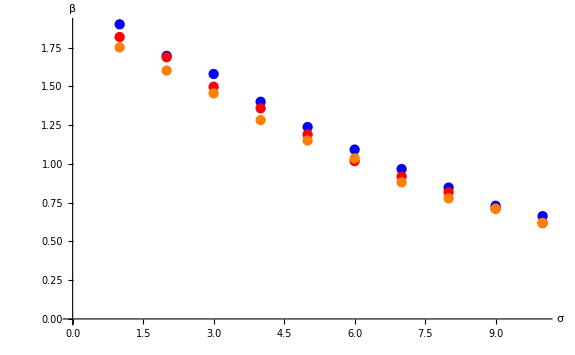

```mathematica
plot100=Show[{ListPlot[betaparameters100[[1]],PlotStyle->Blue],ListPlot[betaparameters100[[2]],PlotStyle->Red],ListPlot[betaparameters100[[3]],PlotStyle->Orange]},AxesLabel->{σ,β}]
```

```mathematica
betaparameters1001={{1.841401131914601,1.7233172982484481,1.5577930659897674,1.4016290608837545,1.276872298582562,1.0785640526456812,0.9685302755809707,0.8502025627600713,0.7202369251526113,0.6683521601119381},{1.8027071006061928,1.6643693300894788,1.5081136762365819,1.3297449632883331,1.1661405344927316,1.03772872800182,0.9218841822990353,0.8130861235567044,0.705849019415666,0.6259605241859979},{1.7392708847528124,1.6023962220526777,1.450273059653412,1.292181113276005,1.1330376297401341,1.0163277655432987,0.9038294665744067,0.7754416416147408,0.6945655592214316,0.60499192337165}};
```

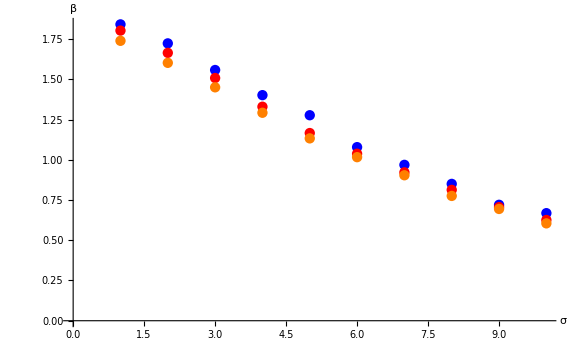

```mathematica
plot100=Show[{ListPlot[betaparameters1001[[1]],PlotStyle->Blue],ListPlot[betaparameters1001[[2]],PlotStyle->Red],ListPlot[betaparameters1001[[3]],PlotStyle->Orange]},AxesLabel->{σ,β}]
```

```mathematica
betaparameters30 = {{1.9383214618149849,1.7512556463688722,1.577247920892056,1.385324926130759,1.2758067635423627,1.0639017949987566,0.9786741036223734,0.8269282528509645,0.7176972912877204,0.6654340288191795},{1.8352245832880325,1.6197868426080182,1.5178332318647982,1.3430954027804698,1.169372918058239,1.0416214995329218,0.8774433067011597,0.7982066255888962,0.6948565452055351,0.593290093114819},{1.7546662538489113,1.6345081440956208,1.4636483246960015,1.3062629637303504,1.170428102876805,1.0313180347128157,0.8653348391631654,0.7660250869283446,0.7128937259806745,0.6220770123347207}};
```

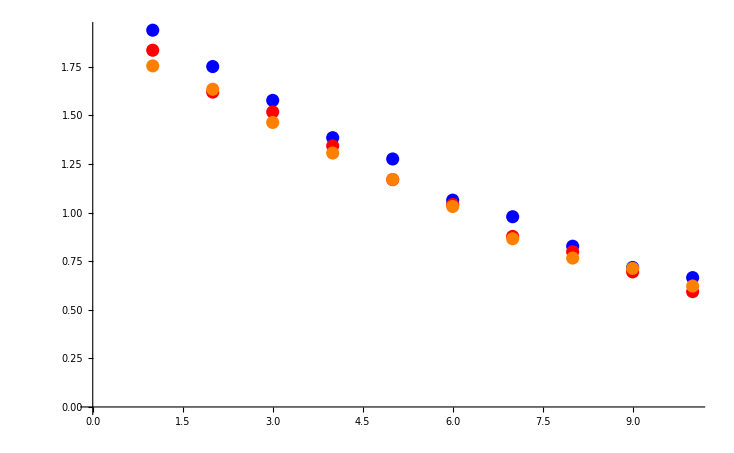

```mathematica
plot30=Show[{ListPlot[betaparameters[[1]],PlotStyle->Blue],ListPlot[betaparameters[[2]],PlotStyle->Red],ListPlot[betaparameters[[3]],PlotStyle->Orange]}]
```